## Intialization Functions

```mathematica
posT1[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,pt1}, (*Position where particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV];
pt1=Flatten[p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2]]

velT1[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,vt1},(*Velocity when particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV];
vt1=Flatten[(v0+({{Cos[θ]}, {Sin[θ]}})*t1*mA)]]
computet1[θ_,v0_,mA_,mV_]:=Module[{t1,vx0,vy0}, (*If the particle is moved with maximum acceleration in direction θ until max velocity is achieved, t1 is when the particle speed is mV.  s default to +1, the positive root*)
{vx0,vy0}=v0;
t1=1/mA(-(vx0 Cos[θ]+vy0 Sin[θ])+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))]
```

### LEAD PHOTO! (Fig. 1)

```mathematica
Row[Table[
If[ i == 1,
p0 = {1,1};
v0 ={-1/2,-1/2};
pG = {0,-0.5};
vG =  {-0.5,0.5};   (*vresion finalVelSolsc1 *) 
mA = 1/2;
,
p0 = {1,1};
v0 ={-1/2,-1/2};
pG = {0,-0.5};
vG =  {-0.5,0.5};   (*vresion finalVelSolsc1 *) 
mA = 1;
];
(*vG = {0,0};  (*version zeroFVelSolss1 *)*)

angD = -135;
(*{Cos[angD °],Sin[angD °]};*)
mV = 1;

fontsz = 14;
{v0x,v0y}=v0;
{p0x,p0y}=p0;
{pGx,pGy}=pG;
{vGx,vGy}=vG;
midPt = (p0+Normalize[v0]*1/2*Norm[v0]^2 /mA +pG -Normalize[vG]*1/2*Norm[vG]^2 /mA)/2; 
pts = {p0,p0+1/2*Normalize[v0]*Norm[v0]^2 /mA ,midPt, pG -1/2*Normalize[vG]*Norm[vG]^2 /mA,pG};
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦5⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦1⟧,-vG,mA];

Quiet[ansFR=FindRoot[  (*This is a numeric solver -- we are searching for an approximate answer.*)
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}]];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["first try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1b,solθ1b,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦4⟧,v0,mA];
{solt2b,solθ2b,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦2⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1b},{τ,solt2b},{θ,solθ1b},{ϕ,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["second try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1,solt1b},{τ,solt2,solt2b},{θ,solθ1,solθ1b},{ϕ,solθ2,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["third try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦3⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦3⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];
t2 = 0;


 maxV = Norm[twoBangBangV[p0,v0,t,τ,θ,ϕ,t,mA]];
If[  maxV >mV,
{θ,ϕ}=numSolveStartAndEndVel2[p0,pG,v0,vG,mA,mV,1,ϕ];
{t,t2,τ}=calctmVV[p0,pG,v0,vG,mA,mV,θ,ϕ];
];

traj = Table[Flatten[posVV[tp,p0,pG,v0,mA,mV,θ1,θ2,{t1,t2,t3}]],{tp,0,tMax,tMax/100.0}];
ParametricPlot[
{posT1[tim 2 π,p0,v0,mA,mV],
posT1[tim 2 π,pG,-vG,mA,mV],posVV[tim(t+t2+τ),p0,pG,v0,mA,mV,θ,ϕ,{t,t2,τ}]},

{tim,0,1},TicksStyle->fontsz,PlotStyle->{Automatic,Automatic,Directive[Thick,Red]},
Epilog->{{PointSize[Medium],Blue,Point[p0],Arrowheads[0.04],Arrow[{p0,p0+v0}],Darker[Green],Point[pG],Arrow[{pG,pG+vG}]}

,Black,Point[posVV[(t  ),p0,pG,v0,mA,mV,θ,ϕ,{t,t2,τ}]]
,Point[posVV[(t+t2  ),p0,pG,v0,mA,mV,θ,ϕ,{t,t2,τ}]]
}
,Prolog->{Arrowheads[0.03],Thin,
Table[pθt1=Flatten[posT1[θv,p0,v0,mA,mV]] ;vθt1=Flatten[velT1[θv,p0,v0,mA,mV]];{LightGray,HalfLine[{pθt1,pθt1+vθt1}],Pink,  Arrow[{pθt1,pθt1+vθt1}]},{θv,-π,π,π/16}],
Table[pθt1=Flatten[posT1[θv,pG,-vG,mA,mV]] ;vθt1=Flatten[velT1[θv,pG,-vG,mA,mV]];{Lighter[Orange],{Dashed,HalfLine[{pθt1,pθt1+vθt1}]},Darker[Orange],  Arrow[{pθt1+vθt1,pθt1}]},{θv,-π,π,π/16}]

} (*,
 PlotLabel->Style[StringForm["|v_0|=1/2, angle ``°",angD],fontsz]*)
,PlotRange->2{{-1,1},{-1,1}},ImageSize->200,Axes->True],{i  ,2}]]
```

-Graphics--Graphics-

## Figure for paper showing the arrows (p(t_1), Fig 3)

```mathematica
p0 = {0,0};
mV = 1;
mA = 1;
fontsz = 14;
Row[Table[
v0 ={vv,vv}; (*compute the initial velocity*)
ParametricPlot[{ posT1[θ,p0,v0,mA,mV]
},{θ,-π,π},TicksStyle->Directive[fontsz],
Epilog->{PointSize[Medium],Blue,Point[p0],Arrowheads[0.04],Arrow[{p0,p0+v0}]}
,Prolog->{Arrowheads[0.03],
Table[pθt1=Flatten[posT1[θv,p0,v0,mA,mV]] ;vθt1=Flatten[velT1[θv,p0,v0,mA,mV]];{LightGray,HalfLine[{pθt1,pθt1+vθt1}],Pink,  Arrow[{pθt1,pθt1+vθt1}]},{θv,-π,π,π/16}]
} ,
 PlotLabel->Style[StringForm["v_0 = ``[1,1]",vv],Directive[Black,fontsz]]
,PlotRange->2{{-1,1},{-1,1}},ImageSize->200,Axes->True],{ vv,{0.01,0.25,0.5,0.707}(*{1/64,1/4,1/2,1/√2}*)}]]
```

-Graphics--Graphics--Graphics--Graphics-

### Caption: Locus of positions where the particle reaches $m_v = 1$. Top row shows four different starting velocities (medium blue). The velocity of the particle due to 32 equally spaced thrust $a_M=1$ in directions $\theta \in \frac{k}{16}\pi$ is shown with pink arrows, all of length $m_v$. These arrows point in every direction. The bottom row shows $v_M = [1/2,1/2]$ for four values of $a_M$.

```mathematica
N[1/√2]
```

0.707107

```mathematica
Length[Range[-π,π,π/16]]
```

33

```mathematica
p0 = {0,0};
mV = 1;
mA = 1;
fontsz = 14;
vv=1/2;
Row[Table[
v0 ={vv,vv}; (*compute the initial velocity*)
ParametricPlot[{ posT1[θ,p0,v0,mA,mV]
},{θ,-π,π},TicksStyle->fontsz,
Epilog->{PointSize[Medium],Blue,Point[p0],Arrowheads[0.04],Arrow[{p0,p0+v0}]}
,Prolog->{Arrowheads[0.03],
Table[pθt1=Flatten[posT1[θv,p0,v0,mA,mV]] ;vθt1=Flatten[velT1[θv,p0,v0,mA,mV]];{LightGray,HalfLine[{pθt1,pθt1+vθt1}],Pink,  Arrow[{pθt1,pθt1+vθt1}]},{θv,-π,π,π/16}]
} ,
 PlotLabel->Style[StringForm["a_M = ``",mA],Directive[Black,fontsz]]
,PlotRange->2{{-1,1},{-1,1}},ImageSize->200,Axes->True],{ mA,{0.4,0.5,1,2}}]]
```

-Graphics--Graphics--Graphics--Graphics-

## Show stopping at goal (Fig. 3)

```mathematica
iterations = 12;
Row[Table[
pG = {0,-1};
vG = {0,0};(*vG = {-0.5,-0};*)
angD = -135;
v0 = {-1/2,-1/2};(*{Cos[angD °],Sin[angD °]};*)
mV = 1;
mA = 1;
fontsz = 14;
If[p0 == {1,1},v0 = {-1,0}];
{θ1,θ2}=numSolveStartAndEndVel[p0,pG,v0,vG,mA,mV,iterations];
{t1,t2,t3}= calctmVV[p0,pG,v0,vG,mA,mV,θ1,θ2];
tMax=t1+t2+t3;
traj = Table[Flatten[posVV[tp,p0,pG,v0,mA,mV,θ1,θ2,{t1,t2,t3}]],{tp,0,tMax,tMax/100.0}];
ParametricPlot[{ posT1[θ,p0,v0,mA,mV], posT1[θ,pG,-vG,mA,mV]
},{θ,-π,π},TicksStyle->fontsz,
Epilog->{{Red,Thick,Line[traj]},{PointSize[Medium],Blue,Point[p0],Arrowheads[0.04],Arrow[{p0,p0+v0}],Darker[Green],Point[pG],Arrow[{pG,pG+vG}]}, Black, Point[posT1[θ1,p0,v0,mA,mV]],Point[posT1[θ2,pG,-vG,mA,mV]]
}
,Prolog->{Arrowheads[0.03],Thin,
Table[pθt1=Flatten[posT1[θv,p0,v0,mA,mV]] ;vθt1=Flatten[velT1[θv,p0,v0,mA,mV]];{LightGray,HalfLine[{pθt1,pθt1+vθt1}],Pink,  Arrow[{pθt1,pθt1+vθt1}]},{θv,-π,π,π/16}],
Table[pθt1=Flatten[posT1[θv,pG,-vG,mA,mV]] ;vθt1=Flatten[velT1[θv,pG,-vG,mA,mV]];{Lighter[Orange],{Dashed,HalfLine[{pθt1,pθt1+vθt1}]},Darker[Orange],  Arrow[{pθt1+vθt1,pθt1}]},{θv,-π,π,π/16}]

} (*,
 PlotLabel->Style[StringForm["|v_0|=1/2, angle ``°",angD],fontsz]*)
,PlotRange->2{{-1,1},{-1,1}},ImageSize->200,Axes->True],{p0  ,{{-1,0},{-1,1},{0,1},{1,1}}}]]
```

-Graphics--Graphics--Graphics--Graphics-

### (Fig. 4 caption) Solution with nonzero starting and zero ending velocity. The locus of positions where the particle reaches $v_m = 1$ from the initial position are shown with a blue set for $p(t_1)$. A similar set constructed starting from the goal position is shown in orange. The solution trajectory is drawn in red. The positions where thrust 1 stops and thrust 2 starts are indicated by black dots. Top row shows four different initial positions with $v_0 = [-0.5,-0.5]$ and $a_m = 1/2$. The system never reaches terminal velocity. Bottom row shows the same positions and velocities, but with $a_m = 1$, so each requires a coasting phase. (Fig. 5 Caption) Solution with nonzero starting and ending velocity. The locus of positions where the particle reaches $v_m = 1$ from the initial position are shown with a blue set for $p(t_1)$. A similar set constructed starting from the goal position using $-v_G$ is shown in orange. The solution trajectory is drawn in red. The positions where thrust 1 stops and thrust 2 starts are indicated by black dots. Top row shows four different initial positions with $v_0 = [-0.5,-0.5]$, $v_G = [-0.5,0]$ and $a_m = 1/2$. The system never reaches terminal velocity. Bottom row shows the same positions and velocities, but with $a_m = 1$. The system reaches terminal velocity $v_m$ in each case.

## Show stopping at goal (Fig. 5)

```mathematica
Row[Table[
pG = {0,-1};
(*vG = {0,0};  (*version zeroFVelSolss1 *)*)
vG =  {-0.5,-0};   (*vresion finalVelSolsc1 *) 
angD = -135;
v0 = v0 = {-1/2,-1/2};(*{Cos[angD °],Sin[angD °]};*)
mV = 1;
mA = 1/2;  (*1 for the other row*)
fontsz = 14;
If[p0 == {1,1} && mA == 1/2,v0 = {-1,0}];
{v0x,v0y}=v0;
{p0x,p0y}=p0;
{pGx,pGy}=pG;
{vGx,vGy}=vG;
midPt = (p0+Normalize[v0]*1/2*Norm[v0]^2 /mA +pG -Normalize[vG]*1/2*Norm[vG]^2 /mA)/2; 
pts = {p0,p0+1/2*Normalize[v0]*Norm[v0]^2 /mA ,midPt, pG -1/2*Normalize[vG]*Norm[vG]^2 /mA,pG};
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦5⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦1⟧,-vG,mA];

Quiet[ansFR=FindRoot[  (*This is a numeric solver -- we are searching for an approximate answer.*)
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}]];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["first try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1b,solθ1b,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦4⟧,v0,mA];
{solt2b,solθ2b,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦2⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1b},{τ,solt2b},{θ,solθ1b},{ϕ,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["second try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1,solt1b},{τ,solt2,solt2b},{θ,solθ1,solθ1b},{ϕ,solθ2,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["third try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦3⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦3⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];
t2 = 0;


 maxV = Norm[twoBangBangV[p0,v0,t,τ,θ,ϕ,t,mA]];
If[  maxV >mV,
(*call the other function!*)
(*If[maxV >2mV,
{θ,ϕ}=numSolveStartAndEndVel[p0,pG,v0,vG,mA,mV,3];,
{θ,ϕ}=numSolveStartAndEndVel2[p0,pG,v0,vG,mA,mV,3,ϕ]];
(*{θ,ϕ}=numSolveStartAndEndVel2[p0,pG,v0,vG,mA,mV,3,ϕ];*)
(*{θ,ϕ}=numSolveStartAndEndVel[p0,pG,v0,vG,mA,mV,3];*)
*)
{θ,ϕ}=numSolveStartAndEndVel2[p0,pG,v0,vG,mA,mV,1,ϕ];
{t,t2,τ}=calctmVV[p0,pG,v0,vG,mA,mV,θ,ϕ];
];

traj = Table[Flatten[posVV[tp,p0,pG,v0,mA,mV,θ1,θ2,{t1,t2,t3}]],{tp,0,tMax,tMax/100.0}];
ParametricPlot[
{posT1[tim 2 π,p0,v0,mA,mV],
posT1[tim 2 π,pG,-vG,mA,mV],posVV[tim(t+t2+τ),p0,pG,v0,mA,mV,θ,ϕ,{t,t2,τ}]},

{tim,0,1},TicksStyle->fontsz,PlotStyle->{Automatic,Automatic,Directive[Thick,Red]},
Epilog->{{PointSize[Medium],Blue,Point[p0],Arrowheads[0.04],Arrow[{p0,p0+v0}],Darker[Green],Point[pG],Arrow[{pG,pG+vG}]}

,Black,Point[posVV[(t         ),p0,pG,v0,mA,mV,θ,ϕ,{t,t2,τ}]],
Point[posVV[(t  +t2       ),p0,pG,v0,mA,mV,θ,ϕ,{t,t2,τ}]]  (*draw second switching time*)
}
,Prolog->{Arrowheads[0.03],Thin,
Table[pθt1=Flatten[posT1[θv,p0,v0,mA,mV]] ;vθt1=Flatten[velT1[θv,p0,v0,mA,mV]];{LightGray,HalfLine[{pθt1,pθt1+vθt1}],Pink,  Arrow[{pθt1,pθt1+vθt1}]},{θv,-π,π,π/16}],
Table[pθt1=Flatten[posT1[θv,pG,-vG,mA,mV]] ;vθt1=Flatten[velT1[θv,pG,-vG,mA,mV]];{Lighter[Orange],{Dashed,HalfLine[{pθt1,pθt1+vθt1}]},Darker[Orange],  Arrow[{pθt1+vθt1,pθt1}]},{θv,-π,π,π/16}]

} (*,
 PlotLabel->Style[StringForm["|v_0|=1/2, angle ``°",angD],fontsz]*)
,PlotRange->2{{-1,1},{-1,1}},ImageSize->200,Axes->True],{p0  ,{{-1,0},{-1,1},{0,1},{1,1}}}]]
```

-Graphics--Graphics--Graphics--Graphics-

## Other math (not in paper)

## Try to match a pt1

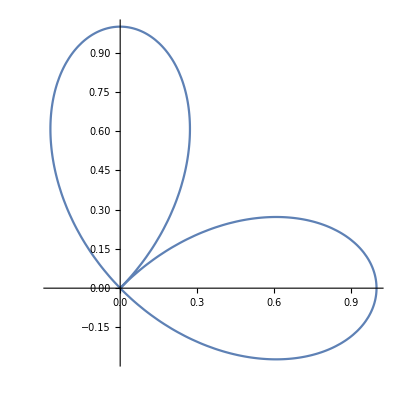

```mathematica
PolarPlot[ Cos[2θ],{θ,π/4,-3/4π}]  (**)
```

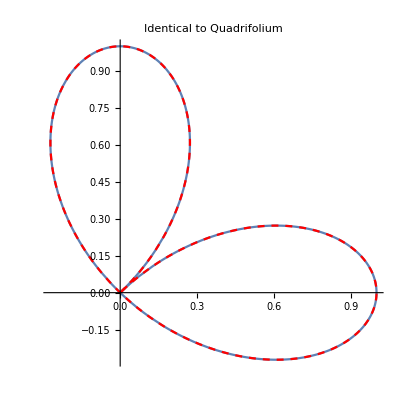

```mathematica
Show[ParametricPlot[{ posT1[θ,{0,0},{1/√2,1/√2},1,1]
},{θ,-π,π}], PolarPlot[ Cos[2θ],{θ,π/4,-3/4π},PlotStyle->Directive[Dashed,Red]],PlotLabel->"Identical to Quadrifolium"]
```

```mathematica
Manipulate[PolarPlot[a*Sign[Cos[2θ]]+(1-a) Cos[2θ],{θ,π/4,-3/4π}],{{a,0},-1,1}]
```

```mathematica
Manipulate[Show[ParametricPlot[{ posT1[θ,{0,0},v0{1,1},1,1]
},{θ,-π,π}],PolarPlot[ (a*Sign[Cos[2θ]]+(1-a) Cos[2θ])/(1+a),{θ,π/4,-3/4π},PlotStyle->Directive[Dashed,Red]]],{{a,0},0,1},{{v0,1/√2},0,1/√2}]
```

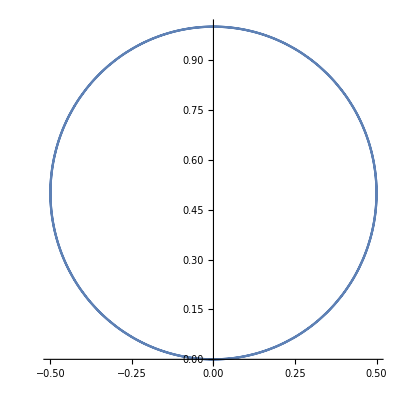

```mathematica
PolarPlot[ Sin[θ],{θ,-π,π}]  (**)
```

```mathematica
(*Epitrochoid*)
Manipulate[ParametricPlot[{(a+b)Cos[t]-h Cos[(a+b)/b t],(a+b)Sin[t]-h Sin[(a+b)/b t]},{t,-2π,2π},PlotRange->All],{a,0,1},{{b,1},0.1,1},{{h,1},0,1}]
```

```mathematica
convertToFindAnalytical[p0_,pG_,v0_,mA_,mV_]:=Module[{θTrans,p0Trans,ϕ, θs,vx0Trans,p0TransRot,solθ,maxError,sError},
(* Finds the orientation to accelerate in so that the system will be able to (eventually) brake to stop at pG.
Inputs: initial position p0, goal position pG, and initial velocity v0, and velocity bound mV and acceleration bound mA.
Returns: solθ, the angle we should apply maximum acceleration in. *)
(*translate so pG is at {0,0}.*)
p0Trans = p0-pG;
vx0Trans =√(v0⟦1⟧^2+v0⟦2⟧^2) ;
(*Print[{N[p0TransRot],vx0Trans,mA,mV}];*)
If[vx0Trans==0,(*Special case: 0 velocity *)
solθ=ArcTan[-p0Trans⟦1⟧,-p0Trans⟦2⟧],
(*rotate so velocity points along x-axis*)
ϕ = -ArcTan[v0⟦1⟧,v0⟦2⟧];
p0TransRot = {
Cos[ϕ]*p0Trans⟦1⟧-Sin[ϕ]*p0Trans⟦2⟧,
 Sin[ϕ]*p0Trans⟦1⟧+Cos[ϕ]*p0Trans⟦2⟧};
If[p0TransRot⟦2⟧==0  (*Special case: the velocity points toward or away from the goal*) ,
θTrans= {0,π },
θTrans=Flatten[analyticalSolutionsθ[N[p0TransRot],N[vx0Trans],N[mA],N[mV]]]
];
(*θTrans=Flatten[analyticalSolutionsθ[N[p0TransRot],N[vx0Trans],N[mA],N[mV]]];*)
(*θTrans= Flatten[analyticalSolutionsθ[p0TransRot,vx0Trans,mA,mV]];*)
(*see if any solutions work.  If so, rotate solutions back to original heading*)
(*Print[{ϕ,θTrans}];*)
maxError = 1000;
solθ = θTrans⟦1⟧;
Table[sError=AnalyticalSolError[p0,pG,v0,mA,mV,Re[θ-ϕ]];
 If[sError<maxError,
maxError=sError;
 solθ=θ-ϕ (*rotate the angle into the original coordinate frame.*)
],{θ,θTrans}];
solθ
]]

AnalyticalSolError[p0_,pG_,v0_,mA_,mV_,θ_]:=Module[{vt1,pt1},
(*given the angle θ, see if at time t1 the velocity lines up with the position error*)
pt1=posT1[θ,p0,v0,mA,mV];
vt1=velT1[θ,p0,v0,mA,mV];
Re[(ArcTan[vt1⟦1⟧,vt1⟦2⟧]-ArcTan[pG⟦1⟧-pt1⟦1⟧,pG⟦2⟧-pt1⟦2⟧])^2]
]


analyticalSolutionsθ[{px0_,py0_},vx0_,mA_,mV_]:=Module[
(*given an initial position {px0,py0} and a goal position of {0,0}, and initial velocity is only in vx0 direction, determines what angle we should apply acceleration mA in so we can eventually brake and stop at {0,0}.  
This requires mV so that we know when we will need to brake.
*)
{sθpc,sθnc,θs,nRoots,
c6,c5,c4,c3,c2,c1,c0},
c0 = Chop[16 mA^4 mV^4 py0^4];c1 =Chop[64 mA^3 mV^4 py0^3 vx0^2] ;c2=Chop[(-32 mA^4 mV^4 px0^2 py0^2-32 mA^4 mV^4 py0^4-8 mA^2 mV^6 py0^2 vx0^2-32 mA^4 mV^2 px0^2 py0^2 vx0^2-32 mA^4 mV^2 py0^4 vx0^2+80 mA^2 mV^4 py0^2 vx0^4-8 mA^2 mV^2 py0^2 vx0^6)] ;

c3=Chop[(-96 mA^3 mV^4 py0^3 vx0^2-16 mA mV^6 py0 vx0^4-96 mA^3 mV^2 py0^3 vx0^4+32 mA mV^4 py0 vx0^6-16 mA mV^2 py0 vx0^8) ];c4=Chop[(16 mA^4 mV^4 px0^4+32 mA^4 mV^4 px0^2 py0^2+16 mA^4 mV^4 py0^4-8 mA^2 mV^6 px0^2 vx0^2-32 mA^4 mV^2 px0^4 vx0^2+8 mA^2 mV^6 py0^2 vx0^2+32 mA^4 mV^2 py0^4 vx0^2+mV^8 vx0^4+8 mA^2 mV^4 px0^2 vx0^4+16 mA^4 px0^4 vx0^4-72 mA^2 mV^4 py0^2 vx0^4+32 mA^4 px0^2 py0^2 vx0^4+16 mA^4 py0^4 vx0^4-4 mV^6 vx0^6+8 mA^2 mV^2 px0^2 vx0^6-72 mA^2 mV^2 py0^2 vx0^6+6 mV^4 vx0^8-8 mA^2 px0^2 vx0^8+8 mA^2 py0^2 vx0^8-4 mV^2 vx0^10+vx0^12) ];c5=Chop[(32 mA^3 mV^4 px0^2 py0 vx0^2+32 mA^3 mV^4 py0^3 vx0^2+8 mA mV^6 py0 vx0^4-64 mA^3 mV^2 px0^2 py0 vx0^4+64 mA^3 mV^2 py0^3 vx0^4-8 mA mV^4 py0 vx0^6+32 mA^3 px0^2 py0 vx0^6+32 mA^3 py0^3 vx0^6-8 mA mV^2 py0 vx0^8+8 mA py0 vx0^10) ];c6=Chop[(16 mA^2 mV^4 px0^2 vx0^4+16 mA^2 mV^4 py0^2 vx0^4-32 mA^2 mV^2 px0^2 vx0^6+32 mA^2 mV^2 py0^2 vx0^6+16 mA^2 px0^2 vx0^8+16 mA^2 py0^2 vx0^8) ];
If[c6≠0,nRoots=6,
If[c5 ≠ 0,nRoots=5,
If[c4≠0,nRoots=4,
If[c3≠ 0,nRoots = 3,
If[c2 ≠ 0,nRoots=2,
If[c1≠0,nRoots=1]]]]]];
sθpc=Table[Root[c0+c1 #1+c2  #1^2+c3  #1^3+c4  #1^4+c5  #1^5+c6  #1^6&,k],{k,1,nRoots}];
(*Are the last 2 roots always imaginary? That's why I'm only picking the first 4... is that justifiable? No: we must check all 6.  When the solution is very close they are not all imaginary.

However, sometimes there aren't 6 roots, for instance with final velocity 0.  Can I ask for all that exist?
I think this only happens when you are perpendicular to the v0 vector, on the line at -v0

*)
(*the negative Cosine[θ] solutions are exactly the same.  Weird. *)
(*sθnc=Table[Root[vx0^4 (-mV^2+vx0^2)^4 #1^4+8 mA py0 vx0^4 (mV^2-vx0^2)^2 #1^3 (-2 mV^2+(mV^2+vx0^2) #1^2)+32 mA^3 py0 vx0^2 #1 (2 mV^4 py0^2-3 mV^2 py0^2 (mV^2+vx0^2) #1^2+(mV^4 (px0^2+py0^2)+2 mV^2 (-px0^2+py0^2) vx0^2+(px0^2+py0^2) vx0^4) #1^4)+8 mA^2 vx0^2 #1^2 (-mV^2 py0^2 (mV^4-10 mV^2 vx0^2+vx0^4)+(mV^2+vx0^2) (mV^4 (-px0^2+py0^2)+2 mV^2 (px0^2-5 py0^2) vx0^2+(-px0^2+py0^2) vx0^4) #1^2+2 vx0^2 (mV^4 (px0^2+py0^2)+2 mV^2 (-px0^2+py0^2) vx0^2+(px0^2+py0^2) vx0^4) #1^4)+16 mA^4 ((px0^2+py0^2)^2 vx0^4 #1^4+mV^4 (py0^2-(px0^2+py0^2) #1^2)^2-2 mV^2 vx0^2 #1^2 (py0^2 (px0^2+py0^2)+(px0^4-py0^4) #1^2))&,k],{k,1,6}];*)
(*θs =Join[Table[ArcTan[√(1- sθ^2),sθ],{sθ,sθpc}],Table[ArcTan[-√(1- sθ^2),sθ],{sθ,sθnc}]]*)
θs =Join[Table[ArcTan[√(1- sθ^2),sθ],{sθ,sθpc}],Table[ArcTan[-√(1- sθ^2),sθ],{sθ,sθpc}]]
]


totalTime[t1_,θ_,p0_,pG_,v0_,mA_,mV_]:=Module[{t2, r,d,t3,posDIFFt1},
r = mV^2/(2 mA); (*Radius of braking circle*)
posDIFFt1 = pG-(p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2);
d = Norm[posDIFFt1];
t2 = (d-r)/mV;(*coasting time*)
t3 = mV/mA;(*braking time*)
t1+t2+t3
]


posT1[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,pt1}, (*Position where particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV];
pt1=Flatten[p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2]]

velT1[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,vt1},(*Velocity when particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV];
vt1=Flatten[(v0+({{Cos[θ]}, {Sin[θ]}})*t1*mA)]]

computet1[θ_,v0_,mA_,mV_]:=Module[{t1,vx0,vy0}, (*If the particle is moved with maximum acceleration in direction θ until max velocity is achieved, t1 is when the particle speed is mV.  s default to +1, the positive root*)
{vx0,vy0}=v0;
t1=(-(vx0 Cos[θ]+vy0 Sin[θ])+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))/mA] 

pos[t_,t1_,θ_,p0_,pG_,v0_,mA_,mV_]:=Module[{t2, r,d,t3,posDIFFt1},
r = mV^2/(2 mA); (*Radius of braking circle*)
posDIFFt1 = pG-(p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2);
d = Norm[posDIFFt1];
t2 = (d-r)/mV;(*coasting time*)
t3 = mV/mA;(*braking time*)
Flatten[p0+t*v0+Piecewise[{{mA/2*({{Cos[θ]}, {Sin[θ]}})*t^2, t<t1}, {mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2+(t-t1)*(({{Cos[θ]}, {Sin[θ]}})*t1*mA), t<t1+t2}, {mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2+(t-t1)*(({{Cos[θ]}, {Sin[θ]}})*t1*mA)+mA/2*(t-t1-t2)^2(-posDIFFt1/d), t<t1+t2+t3}, {-t*v0+pG-p0, True}}]]]
vel[t_,t1_,θ_,p0_,pG_,v0_,mA_,mV_]:=Module[{t2, r,d,t3,posDIFFt1},
r = mV^2/(2 mA); (*Radius of braking circle*)
posDIFFt1 = pG-(p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2);
d = Norm[posDIFFt1];
 t2 = (d-r)/mV;(*coasting time*)
t3 = mV/mA;(*braking time*)
Flatten[v0+Piecewise[{{mA*({{Cos[θ]}, {Sin[θ]}})*t, t<t1}, {mA*({{Cos[θ]}, {Sin[θ]}})*t1, t<t1+t2}, {mA*({{Cos[θ]}, {Sin[θ]}})*t1+mA*(t-t1-t2)(-posDIFFt1/d), t<t1+t2+t3}, {-v0, True}}]]]
acc[t_,t1_,θ_,p0_,pG_,v0_,mA_,mV_]:=Module[{t2, r,d,t3,posDIFFt1},
r = mV^2/(2 mA); (*Radius of braking circle*)
posDIFFt1 = pG-(p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2);
d = Norm[posDIFFt1];
 t2 = (d-r)/mV;(*coasting time*)
t3 = mV/mA;(*braking time*)
Flatten[Piecewise[{{mA*({{Cos[θ]}, {Sin[θ]}}), t<t1}, {({{0}, {0}}), t<t1+t2}, {mA*(-posDIFFt1/d), t<t1+t2+t3}, {({{0}, {0}}), True}}]]]
(*numSolveStartAndEndVel[p0,pG,v0,vG,mA,mV,3];(*t,τ,θ,ϕ*)*)
numSolveStartAndEndVel2[p0_,pG_,v0_,vG_,mA_,mV_,iterations_:1,ϕ_]:=Module[{θ1,pT1,θ2,pT2,pS1,pS2,err,iter=0,t1,t2,t3},
(*Returns {θ1,θ2}, the angles for the two bang bang inputs. The system coasts in between.  This version starts with a guess for the angle ϕ at the end when starting from pG with velocity -vG. ϕ should be calculated using the no-coasting assumption.
*)
(*pS1 = p0+Norm[v0]^2/(2 mA)Normalize[v0];(*Stopping point with full braking starting at p0*)
pS2 = pG-Norm[vG]^2/(2 mA)Normalize[vG]; (*Stopping point with full braking starting at pG, back in time*)
pT2 =1/2(pS1+pS2)(*+mV^2/(2 mA)Normalize[pS2-pS1]*)(*+Norm[-vG+v0]^2/(2 mA)Normalize[-vG+v0]*);*)
(*Start pT2 at midpoint of stop, accelerate, stop path*)
pT2 =posT1[ϕ,pG,-vG,mA,mV];(*end of coasting position*)
err = 10;
While[err>0.001 && iter <11,
θ1 = convertToFindAnalytical[p0,pT2,v0,mA,mV]; (*Pick θ1 to start at {p0, v0}, finishes at pT2 *)
pT1 =posT1[θ1,p0,v0,mA,mV]; (*start of coasting position*)
θ2 = convertToFindAnalytical[pG,pT1,-vG,mA,mV]; (*Pick θ2 go back in time from {pG,vG} reaches pT1 *)
pT2 =posT1[θ2,pG,-vG,mA,mV];(*end of coasting position*)

(*Calculate the error*)
iter = iter+1;
{t1,t2,t3} = calctmVV[p0,pG,v0,vG,mA,mV,θ1,θ2];

err = Norm[posVV[t1+t2+t3,p0,pG,v0,mA,mV,θ1,θ2,{t1,t2,t3}]-pG];
(*Print[StringForm["iter=``,err = ``",iter,err]];*)
];
(*Print[iter];*)
{θ1,θ2}
]


numSolveStartAndEndVel[p0_,pG_,v0_,vG_,mA_,mV_,iterations_:1]:=Module[{θ1,pT1,θ2,pT2,pS1,pS2},
(*Returns {θ1,θ2}, the angles for the two bang bang inputs. The system coasts in between.*)
(*pT2 =pG-vG; (*Start  pT2 at pG-vG*)*)
pS1 = p0+Norm[v0]^2/(2 mA)Normalize[v0];(*Stopping point with full braking starting at p0*)
pS2 = pG-Norm[vG]^2/(2 mA)Normalize[vG]; (*Stopping point with full braking starting at pG, back in time*)
pT2 =1/2(pS1+pS2)(*+mV^2/(2 mA)Normalize[pS2-pS1]*)(*+Norm[-vG+v0]^2/(2 mA)Normalize[-vG+v0]*);
(*Start pT2 at midpoint of stop, accelerate, stop path*)
pT2 =pG-vG;
Table[
θ1 = convertToFindAnalytical[p0,pT2,v0,mA,mV]; (*Pick θ1 to start at {p0, v0}, finishes at pT2 *)
pT1 =posT1[θ1,p0,v0,mA,mV]; (*start of coasting position*)
θ2 = convertToFindAnalytical[pG,pT1,-vG,mA,mV]; (*Pick θ2 go back in time from {pG,vG} reaches pT1 *)
pT2 =posT1[θ2,pG,-vG,mA,mV];(*end of coasting position*)
,{i,iterations}];
{θ1,θ2}
]

changeCoordinates[p0_,pG_,v0_,vG_,mA_,mV_]:=Module[{p0Trans,vx0Trans,ϕ ,rotϕ,p0TransRot},
(*translate so pG is at {0,0}*)
p0Trans = p0-pG;
vx0Trans =√(v0⟦1⟧^2+v0⟦2⟧^2) ;
ϕ =If[vx0Trans==0,(*Special case: 0 velocity *) 0, -ArcTan[v0⟦1⟧,v0⟦2⟧]]; 
(*rotate so velocity points along x-axis*)
rotϕ = {
{Cos[ϕ],-Sin[ϕ]},
{ Sin[ϕ],+Cos[ϕ]}};
p0TransRot = rotϕ.p0Trans;
(*{p0,pG,v0,vG,ϕ }*)
{p0TransRot,{0,0},{vx0Trans,0}, rotϕ.vG,ϕ }
]

numSolveBBStartAndEndVel[p0_,pG_,v0_,vG_,mA_]:=Module[{midPt,
solt1,solθ1,maxV1, tMax1,solt2,solθ2,maxV2, tMax2,ansFR,p0x,p0y,v0x,v0y,vGx, vGy,pGx,pGy,t1,t2,θ1,θ2},
(*Returns the bang-bang solution (no coasting phase) with the two pairs of angles and times for thrusting:
{t1,θ1,t2,θ2}*)
(*midPt = (p0+v0 /mA +pG -vG/mA)/2; (*TODO: switch to better midpoint*)*)
midPt =(p0+Normalize[v0]Norm[v0]^2 /mA +pG -Normalize[vG]Norm[vG]^2 /mA )/2;
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,midPt,v0,mA];
Print[StringForm["{solt1,solθ1,{maxV1, tMax1}}=``",{solt1,solθ1,{maxV1, tMax1}}]];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[p0,midPt,-vG,mA];
Print[StringForm["{solt2,solθ2,{maxV2, tMax2}}=``",{solt2,solθ2,{maxV2, tMax2}}]];
{p0x,p0y}= p0;
{v0x,v0y}=v0;
{pGx, pGy}=pG;
{vGx, vGy}=vG;
ansFR=FindRoot[
{   p0x+v0x*t1+mA/2 Cos[θ1] t1^2==pGx-vGx*t2+mA/2Cos[θ2] t2^2&&
p0y+v0y*t1+mA/2Sin[θ1] t1^2==pGy-vGy*t2+mA/2Sin[θ2] t2^2&&
v0x + mA*Cos[θ1]t1==vGx -  mA*Cos[θ2]t2&&
v0y + mA*Sin[θ1]t1==vGy -  mA*Sin[θ2]t2}, {{t1,solt1},{t2,solt2},{θ1,solθ1},{θ2,solθ2}}];
Print[StringForm["The error is ``",computeErr[p0,pG,v0,vG,t1,t2,θ1,θ2,mA]/.ansFR]];
{t1,θ1,t2,θ2}/.ansFR   (*incorporate the error term*)
]

(*numSolveBBStartAndEndVel[p0i_,pGi_,v0i_,vGi_,mA_,mVi_]:=Module[{midPt,p0,pG,v0,vG,ϕ,
solt1,solθ1,maxV1, tMax1,solt2,solθ2,maxV2, tMax2,ansFR,p0x,p0y,v0x,vGx, vGy,t1,t2,θ1,θ2,mV},
mV = 100;
(*Returns the bang-bang solution (no coasting phase) with the two pairs of angles and times for thrusting:
{t1,θ1,t2,θ2}
*)
{p0,pG,v0,vG,ϕ }=changeCoordinates[p0i,pGi,v0i,vGi,mA,mV];
midPt = (p0+v0 /mA +pG -vG)/2; (*TODO: switch to better midpoint*)
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,midPt,v0,mA];
Print[StringForm["{solt1,solθ1,{maxV1, tMax1}}=``",{solt1,solθ1,{maxV1, tMax1}}]];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[p0,midPt,-vG,mA];
Print[StringForm["{solt2,solθ2,{maxV2, tMax2}}=``",{solt2,solθ2,{maxV2, tMax2}}]];
{p0x,p0y} = p0;
v0x = v0⟦1⟧;
{vGx, vGy}=vG;
ansFR=FindRoot[
{p0x+v0x*t1+1/2 Cos[θ1] t1^2==-vGx*t2+1/2Cos[θ2] t2^2&&
p0y+1/2Sin[θ1] t1^2==-vGy*t2+1/2Sin[θ2] t2^2&&
v0x +  Cos[θ1]t1==vGx -  Cos[θ2]t2&&
 Sin[θ1]t1==vGy -  Sin[θ2]t2}, {{t1,solt1},{t2,solt2},{θ1,solθ1},{θ2,solθ2}}];
Print[StringForm["The error is ``",computeErr[{p0x,p0y},{0,0},v0x,{vGx,vGy},t1,t2,θ1,θ2]/.ansFR]];
{t1,θ1-ϕ,t2,θ2-ϕ}/.ansFR   (*incorporate the error term*)

]*)

drawRocketThrust[pt_,at_]:=Module[{nat},
nat=Norm[at];
{EdgeForm[None],If[at≠ {0,0}, Rotate[{   (*This is wrong, since it allows us to rotate the thrust*)
Red,        Disk[pt-{.2+nat,0},1.00nat{1,.2}],
Orange ,Disk[pt-{.2+.75nat,0},0.75nat{1,.2}],
Yellow ,Disk[pt-{.2+.4nat,0},0.40nat{1,.2}]},ArcTan[First@at,Last@at],pt]],
Gray,Disk[pt,0.3]
}
]

posAndtAtt1[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,pt1}, (*returns {Position,time} where & when particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV];
pt1=Flatten[p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2];
{t1,pt1}
]

(*Start and stop velocity*)
calctmVV[p0_,pG_,v0_,vG_,mA_,mV_,θ1_,θ2_]:=Module[{t1,pt1,t2,t3,pt3},
{t1, pt1}=posAndtAtt1[θ1,p0,v0,mA,mV];
{t3, pt3}=posAndtAtt1[θ2,pG,-vG,mA,mV];
t2 = Norm[pt1-pt3]/mV;
Chop[{t1,t2,t3}]
]
posVV[t_,p0_,pG_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=
Flatten[p0+t*v0+Piecewise[{{mA/2*({{Cos[θ1]}, {Sin[θ1]}})*t^2, t<t1}, {mA/2*({{Cos[θ1]}, {Sin[θ1]}})*t1^2+(t-t1)*(({{Cos[θ1]}, {Sin[θ1]}})*t1*mA), t<t1+t2}, {mA/2*({{Cos[θ1]}, {Sin[θ1]}})*t1^2+(t-t1)*(({{Cos[θ1]}, {Sin[θ1]}})*t1*mA)+mA/2*(t-t1-t2)^2({{Cos[θ2]}, {Sin[θ2]}}), t<t1+t2+t3}, {mA/2*({{Cos[θ1]}, {Sin[θ1]}})*t1^2+(t-t1)*(({{Cos[θ1]}, {Sin[θ1]}})*t1*mA)+mA/2*(t3)^2({{Cos[θ2]}, {Sin[θ2]}})+(t-t1-t2-t3)*(({{Cos[θ2]}, {Sin[θ2]}})*t3*mA), True}}]]
velVV[t_,p0_,pG_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=
Flatten[v0+Piecewise[{{mA*({{Cos[θ1]}, {Sin[θ1]}})*t, t<t1}, {mA*({{Cos[θ1]}, {Sin[θ1]}})*t1, t<t1+t2}, {mA*({{Cos[θ1]}, {Sin[θ1]}})*t1+mA*(t-t1-t2)({{Cos[θ2]}, {Sin[θ2]}}), t<t1+t2+t3}, {mA*({{Cos[θ1]}, {Sin[θ1]}})*t1+mA*({{Cos[θ2]}, {Sin[θ2]}})*t3, True}}]]
accVV[t_,p0_,pG_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=
Flatten[Piecewise[{{mA*({{Cos[θ1]}, {Sin[θ1]}}), t<t1}, {({{0}, {0}}), t<t1+t2}, {mA*({{Cos[θ2]}, {Sin[θ2]}}), t<t1+t2+t3}, {({{0}, {0}}), True}}]]
```

### Simplify angle of robot at t1

```mathematica
Clear[θ,vx0,vy0,mV,mA,t1]
t1=(-(vx0 Cos[θ]+vy0 Sin[θ])+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))/mA;
(({{vx0}, {vy0}})+({{Cos[θ]}, {Sin[θ]}})*t1*mA)
```

{{vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))},{vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))}}

```mathematica
FullSimplify[(vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)))/(vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)))]
```

(vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)))/(vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)))

```mathematica
Clear[ϕ,vx0,vy0]
```

```mathematica
mV = 1;Clear[ϕ,vx0,vy0,a,θ]
Manipulate[Module[{vx0,vy0},
vx0 =amp Cos[ϕ];vy0 = amp Sin[ϕ];
Plot[ArcTan[vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)), vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))],{θ,-π,+π}]],{amp,0,1},{ϕ,-π,π}]
```

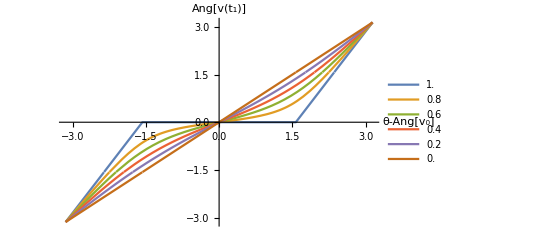

```mathematica
ϕ = 0;
Plot[Evaluate@Table[vx0 =amp Cos[ϕ];vy0 = amp Sin[ϕ];
ArcTan[vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)), vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))],{amp, 1,0,-0.2}],{θ,-π,π},AxesLabel->{"θ-Ang[v_0]","Ang[v(t_1)]"},PlotLegends->Placed[Table[amp,{amp, 1,0,-0.2}],{0.1,0.6}]]
```

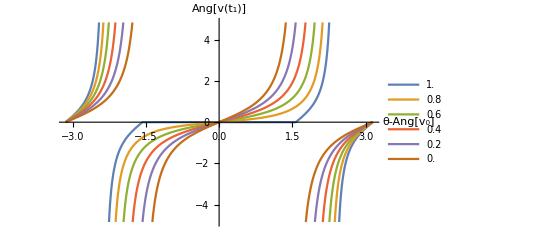

```mathematica
ϕ = 0;
Plot[Evaluate@Table[vx0 =amp Cos[ϕ];vy0 = amp Sin[ϕ];
(vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)))/(vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))),{amp, 1,0,-0.2}],{θ,-π,π},AxesLabel->{"θ-Ang[v_0]","Ang[v(t_1)]"},PlotLegends->Placed[Table[amp,{amp, 1,0,-0.2}],{0.1,0.6}]]
```

```mathematica
Clear[ϕ,vx0,vy0,a,θ,mV]
vx0=Cos[ϕ];
vy0 = Sin[ϕ];
FullSimplify[ArcTan[vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)), vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))]]
```

ArcTan[√2 Cos[θ] √(-1+2 mV^2+Cos[2 (θ-ϕ)])+2 Sin[θ] Sin[θ-ϕ],√2 √(-1+2 mV^2+Cos[2 (θ-ϕ)]) Sin[θ]-2 Cos[θ] Sin[θ-ϕ]]

```mathematica
Clear[ϕ,vx0,vy0,a,θ,mV]
vx0=Cos[ϕ];
vy0 = Sin[ϕ];
mV = 1;
FullSimplify[ArcTan[vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)), vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))]]
```

ArcTan[Cos[θ] √(Cos[θ-ϕ]^2)+Sin[θ] Sin[θ-ϕ],√(Cos[θ-ϕ]^2) Sin[θ]-Cos[θ] Sin[θ-ϕ]]

```mathematica
FullSimplify[(√(Cos[θ-ϕ]^2) Sin[θ]-Cos[θ] Sin[θ-ϕ])/(Cos[θ] √(Cos[θ-ϕ]^2)+Sin[θ] Sin[θ-ϕ])]
```

(√(Cos[θ-ϕ]^2) Sin[θ]-Cos[θ] Sin[θ-ϕ])/(Cos[θ] √(Cos[θ-ϕ]^2)+Sin[θ] Sin[θ-ϕ])

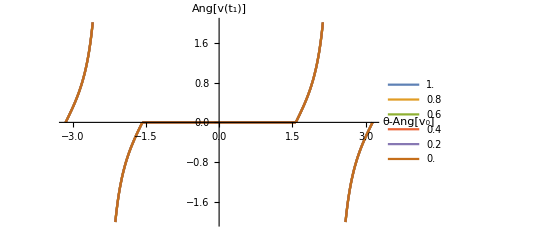

```mathematica
ϕ = 0;
Plot[Evaluate@Table[
(√(Cos[θ-ϕ]^2) Sin[θ]-Cos[θ] Sin[θ-ϕ])/(Cos[θ] √(Cos[θ-ϕ]^2)+Sin[θ] Sin[θ-ϕ]),{amp, 1,0,-0.2}],{θ,-π,π},AxesLabel->{"θ-Ang[v_0]","Ang[v(t_1)]"},PlotLegends->Placed[Table[amp,{amp, 1,0,-0.2}],{0.1,0.6}]]
```

```mathematica
Clear[ϕ,vx0,vy0,a,θ,mV,amp]
vx0=amp Cos[ϕ];
vy0 =amp Sin[ϕ];
FullSimplify[ArcTan[vx0+Cos[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2)), vy0+Sin[θ] (-vx0 Cos[θ]-vy0 Sin[θ]+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))]]
```

ArcTan[Cos[θ] √(-amp^2/2+mV^2+1/2 amp^2 Cos[2 (θ-ϕ)])+amp Sin[θ] Sin[θ-ϕ],√(-amp^2/2+mV^2+1/2 amp^2 Cos[2 (θ-ϕ)]) Sin[θ]-amp Cos[θ] Sin[θ-ϕ]]

```mathematica
FullSimplify[(√(-amp^2/2+mV^2+1/2 amp^2 Cos[2 (θ-ϕ)]) Sin[θ]-amp Cos[θ] Sin[θ-ϕ])/(Cos[θ] √(-amp^2/2+mV^2+1/2 amp^2 Cos[2 (θ-ϕ)])+amp Sin[θ] Sin[θ-ϕ])]
```

(√(-2 amp^2+4 mV^2+2 amp^2 Cos[2 (θ-ϕ)]) Sin[θ]-2 amp Cos[θ] Sin[θ-ϕ])/(Cos[θ] √(-2 amp^2+4 mV^2+2 amp^2 Cos[2 (θ-ϕ)])+2 amp Sin[θ] Sin[θ-ϕ])

```mathematica
TrigToExp[ArcTan[Cos[θ] √(-amp^2/2+mV^2+1/2 amp^2 Cos[2 (θ-ϕ)])+amp Sin[θ] Sin[θ-ϕ],√(-amp^2/2+mV^2+1/2 amp^2 Cos[2 (θ-ϕ)]) Sin[θ]-amp Cos[θ] Sin[θ-ϕ]]]
```

```mathematica
Simplify[-ⅈ Log[(-1/4 amp (ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)) (-ⅇ^(ⅈ θ-ⅈ ϕ)+ⅇ^(-ⅈ θ+ⅈ ϕ))+1/2 (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) √(-amp^2/2+1/4 amp^2 (ⅇ^(-2 ⅈ (θ-ϕ))+ⅇ^(2 ⅈ (θ-ϕ)))+mV^2)+ⅈ (-1/4 ⅈ amp (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) (-ⅇ^(ⅈ θ-ⅈ ϕ)+ⅇ^(-ⅈ θ+ⅈ ϕ))+1/2 ⅈ (ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)) √(-amp^2/2+1/4 amp^2 (ⅇ^(-2 ⅈ (θ-ϕ))+ⅇ^(2 ⅈ (θ-ϕ)))+mV^2)))/(√((-1/4 ⅈ amp (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) (-ⅇ^(ⅈ θ-ⅈ ϕ)+ⅇ^(-ⅈ θ+ⅈ ϕ))+1/2 ⅈ (ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)) √(-amp^2/2+1/4 amp^2 (ⅇ^(-2 ⅈ (θ-ϕ))+ⅇ^(2 ⅈ (θ-ϕ)))+mV^2))^2+(-1/4 amp (ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)) (-ⅇ^(ⅈ θ-ⅈ ϕ)+ⅇ^(-ⅈ θ+ⅈ ϕ))+1/2 (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) √(-amp^2/2+1/4 amp^2 (ⅇ^(-2 ⅈ (θ-ϕ))+ⅇ^(2 ⅈ (θ-ϕ)))+mV^2))^2))]]
```

-ⅈ Log[(ⅇ^(-ⅈ ϕ) (amp (-ⅇ^(2 ⅈ θ)+ⅇ^(2 ⅈ ϕ))+ⅇ^(ⅈ (θ+ϕ)) √(amp^2 ⅇ^(-2 ⅈ (θ+ϕ)) (ⅇ^(2 ⅈ θ)-ⅇ^(2 ⅈ ϕ))^2+4 mV^2)))/(2 √(mV^2))]